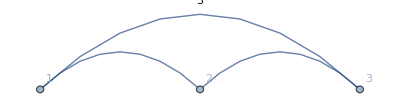
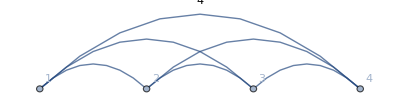
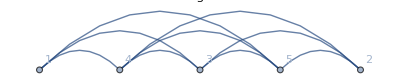
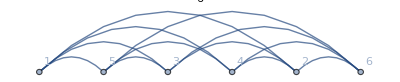
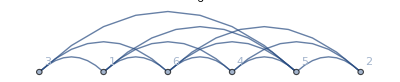
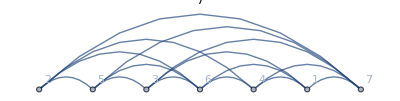
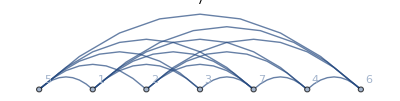
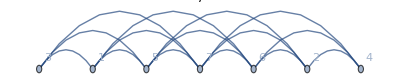

```mathematica
Column[Table[Show[Graph[EdgeList[Graph[GraphData[k]]],GraphLayout->{"PackingLayout"->"NestedGrid","ComponentLayout"-> "LinearEmbedding","RenderingOrder"->"VertexFirst","EdgeLayout"->"HierarchicalEdgeBundling"}, VertexLabels->"Name", PlotLabel->Style[VertexCount[GraphData[k]],Bold,FontSize->20, Red, Background->Lighter[Yellow]]],ImageSize->400],{k,Sort[GraphData["Triangulated"],VertexCount[GraphData[#1]]<VertexCount[GraphData[#2]]&]}]]
```